## Coulomb on a infinite lattice with different spacing

```mathematica
mass=1.0;
```

```mathematica
Clear[dist];
dist[i_,j_]:=Sqrt[i^2+j^2]

Clear[g,a,b,c,latticeCoulomb];
latticeCoulomb[i_,j_,aspace_:1]:=1/2 NIntegrate[Cos[(x*i+y*j)]/(2.0-Cos[x]-Cos[y]+mass^2*aspace^2/2 ),{x,0,2Pi},{y,0,2Pi},Method->"LevinRule"]/(2Pi)^2

Clear[discretizationError];
discretizationError[i_,j_,aspace_:0.1]:=Module[{x,y},
x=N[BesselK[0,dist[i,j]]/(2Pi)];
(* Error get tuned by the spacing *)
y=latticeCoulomb[i/aspace,j/aspace,aspace];
Print[x,y];
y-x
]
```

### test - Indeed, the error is quadratic in lattice spacing! but in terms of momentum cutoff, it is not esay to test (pm^{-3/2}?)

```mathematica
Series[(2/a Sin[p a/2])^2,{a,0,3}]
```

p^2-(p^4 a^2)/12+O[a]^4

```mathematica
data=Table[
{1.3^(n),NIntegrate[Sqrt[p]/(p^2+1)Cos[p-Pi/4],{p,1.3^(n),Infinity},Method->"LevinRule"]},
{n,2,30}]
```

{{1.69,-0.120656},{2.197,-0.181235},{2.8561,-0.159915},{3.71293,-0.0587906},{4.82681,0.0504435},{6.27485,0.0498499},{8.15731,-0.0325749},{10.6045,0.00723787},{13.7858,-0.00619784},{17.9216,0.0127109},{23.2981,0.00390593},{30.2875,0.00552234},{39.3738,-0.00303732},{51.1859,-0.000287935},{66.5417,-0.000437006},{86.5042,0.000956267},{112.455,0.000831222},{146.192,-0.000437081},{190.05,-0.000263139},{247.065,-0.00024258},{321.184,8.44487×10^-6},{417.539,-0.000103467},{542.801,-0.000078769},{705.641,-0.0000484009},{917.333,0.0000257843},{1192.53,0.0000214503},{1550.29,0.0000105757},{2015.38,8.18759×10^-6},{2620.,5.73602×10^-6}}

```mathematica
data=Abs[data]
```

{{1.69,0.120656},{2.197,0.181235},{2.8561,0.159915},{3.71293,0.0587906},{4.82681,0.0504435},{6.27485,0.0498499},{8.15731,0.0325749},{10.6045,0.00723787},{13.7858,0.00619784},{17.9216,0.0127109},{23.2981,0.00390593},{30.2875,0.00552234},{39.3738,0.00303732},{51.1859,0.000287935},{66.5417,0.000437006},{86.5042,0.000956267},{112.455,0.000831222},{146.192,0.000437081},{190.05,0.000263139},{247.065,0.00024258},{321.184,8.44487×10^-6},{417.539,0.000103467},{542.801,0.000078769},{705.641,0.0000484009},{917.333,0.0000257843},{1192.53,0.0000214503},{1550.29,0.0000105757},{2015.38,8.18759×10^-6},{2620.,5.73602×10^-6}}

```mathematica
model=a/pm^b;
fit=FindFit[data[[2;;]],model,{a,b},pm];
modelf=Function[{x},Evaluate[model/.fit]]
```

Function[{x},0.639671/pm^1.5348]

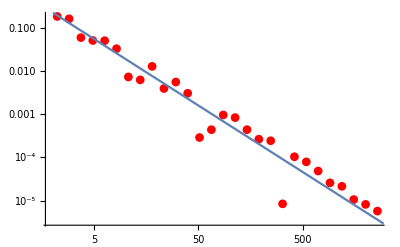

```mathematica
Show[
ListLogLogPlot[
data[[2;;]],PlotStyle->{Red,PointSize[0.05]},PlotMarkers->Automatic
],
LogLogPlot[modelf[t]/.t->pm,{pm,2,3000},PlotRange->Full]
]
```

#### test

```mathematica
data=Table[
{2^(-n),discretizationError[0,1,2^(-n)]},
{n,0,8}]
```

{{1,0.000554177},{1/2,0.00234079},{1/4,0.000538786},{1/8,0.000106702},{1/16,0.0000253579},{1/32,6.26611×10^-6},{1/64,1.56273×10^-6},{1/128,3.9118×10^-7},{1/256,9.87039×10^-8}}

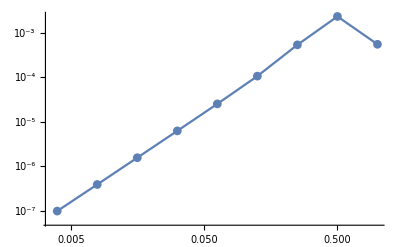

```mathematica
ListLogLogPlot[data,PlotMarkers->Automatic,Joined->True]
```

```mathematica
model=a h^2;
fit=FindFit[data[[2;;]],model,{a,b},h];
modelf=Function[{x},Evaluate[model/.fit]]
```

Function[{x},0.00930968 h^2]

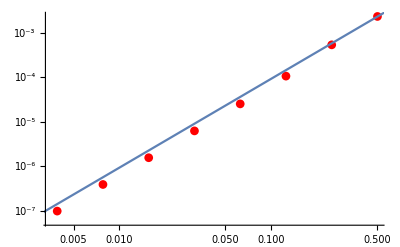

```mathematica
Show[
ListLogLogPlot[
data[[2;;]],PlotStyle->{Red,PointSize[0.05]},PlotMarkers->Automatic
],
LogLogPlot[modelf[t]/.t->h,{h,10^(-3),1}]
]
```

### Probably, this behavior can be used to do extrapolation to a->0.

```mathematica
Series[p^2-(2/a Sin[p a/2])^2,{a,0,4}]
```

(p^4 a^2)/12-(p^6 a^4)/360+O[a]^5

```mathematica
data=N[Table[{a,1-(2/a Sin[a/2])^2}/.a->1/n,{n,1,10}]];
```

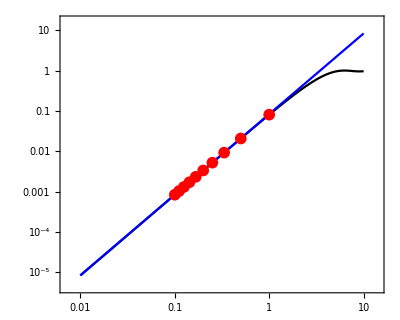

```mathematica
result=Show[
LogLogPlot[{1-(2/a Sin[a/2])^2,a^2/12},{a,10^(-2),10},PlotRange->{0,0.1},PlotStyle->{Black,Blue},
TicksStyle->Directive[Thick,20],Frame->True,GridLines->Automatic,
AspectRatio->0.8],
ListLogLogPlot[data,PlotRange->{0,0.1},PlotStyle->Red,
PlotMarkers->{Automatic,12}]]
```

```mathematica
Export["~/Desktop/discretErr.pdf",result]
```

~/Desktop/discretErr.pdf

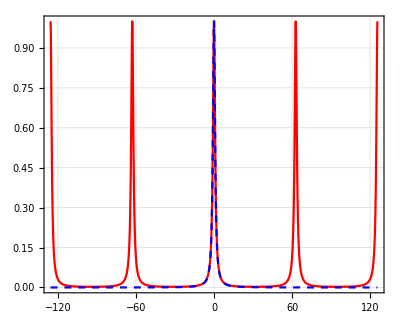

```mathematica
result2=Plot[{((2/a Sin[p a/2])^2+1)^{-1}/.a->0.1,(p^2+1)^{-1}},{p,-4Pi/0.1,4Pi/0.1},PlotRange->{0,1},TicksStyle->Directive[Thick,20],Frame->True,GridLines->Automatic,PlotStyle->{Red,{Blue,Dashed}},AspectRatio->0.8]
```

```mathematica
Export["~/Desktop/latticeMomentum.pdf",result2]
```

~/Desktop/latticeMomentum.pdf

## Plot

```mathematica
rdist={g[0,1],g[0,2],g[0,3],g[0,4],g[0,5]}/.g->dist
vij={g[0,1],g[0,2],g[0,3],g[0,4],g[0,5]}/.g[x_,y_]:>latticeCoulomb2[x,y,0.001]
```

{1,2,3,4,5}

{0.0670081,0.0181268,0.00552896,0.00177612,0.000587456}

```mathematica
ord=Ordering[rdist];
rdistSorted=rdist[[ord]];
vijSorted=vij[[ord]];
```

```mathematica
data=Thread[List[rdistSorted,vijSorted]];
model=a BesselK[0,b x];
fit=FindFit[data,{model,b≥0,a>0},{a,b},x];
modelf=Function[{x},Evaluate[model/.fit]]
```

Function[{x},0.159274 BesselK[0,1.00048 x]]

```mathematica
rdist2={g[1,1],g[1,2],g[2,2]}/.g->dist
vij2={g[1,1],g[1,2],g[2,2]}/.g[x_,y_]:>latticeCoulomb2[x,y,0.001]
```

{√2,√5,2 √2}

{0.0380607,0.0136023,0.00674686}

### error

```mathematica
errMax=Max[Abs[modelf[rdist]-vijSorted]]
errMax=Max[Abs[modelf[rdist2]-vij2]]
```

7.9057×10^-6

7.50795×10^-6

```mathematica
Max[Abs[BesselK[0,mass*0.001*rdist]/(2Pi)-vijSorted]]
Max[Abs[BesselK[0,mass*0.001*rdist2]/(2Pi)-vij2]]
```

1.05085

1.02464

```mathematica
vlst=Sort[Join[data,Thread[List[rdist2,vij2]]],#1[[1]]<#2[[1]]&]
```

{{1,0.0670081},{√2,0.0380607},{2,0.0181268},{√5,0.0136023},{2 √2,0.00674686},{3,0.00552896},{4,0.00177612},{5,0.000587456}}

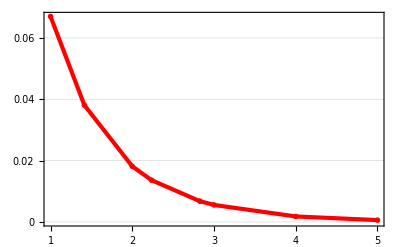

```mathematica
ListPlot[
vlst,PlotStyle->{{Red,PointSize[0.05]},{Blue,PointSize[0.05]}},
PlotTheme->{"Business"},Joined->True
]
```

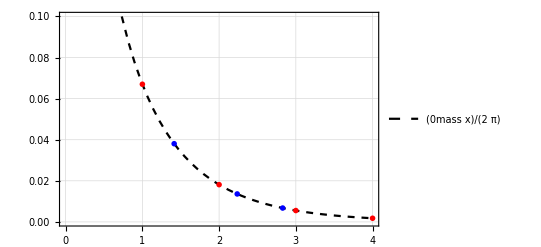

```mathematica
Show[
Plot[
BesselK[0,mass *x]/(2Pi),{x,0,4},PlotRange->{0,0.1},PlotStyle->{Black,Dashed},PlotTheme->{"Detailed"}
],
ListPlot[
{data,Thread[List[rdist2,vij2]]},PlotStyle->{{Red,PointSize[0.05]},{Blue,PointSize[0.05]}},
PlotTheme->{"Business"}
]
]
```

## decay of errors

```mathematica
nmax=10
```

10

```mathematica
vset=Table[g[0,i],{i,1,nmax}];
rdist=vset/.g->dist
vv=vset/.g->latticeCoulomb
```

{1,2,3,4,5,6,7,8,9,10}

{0.0675623,0.0197369,0.00618455,0.00203436,0.000691423,0.000240258,0.0000847844,0.0000302552,0.0000108873,3.94339×10^-6}

### error

```mathematica
defaultSpacing=1
err=Abs[BesselK[0,mass*defaultSpacing*rdist]/(2Pi)-vv]
```

1

{0.000554177,0.00161008,0.000655582,0.000258244,0.000103966,0.0000422703,0.0000171761,6.94366×10^-6,2.78934×10^-6,1.1136×10^-6}

```mathematica
vv
```

{0.0675623,0.0197369,0.00618455,0.00203436,0.000691423,0.000240258,0.0000847844,0.0000302552,0.0000108873,3.94339×10^-6}

```mathematica
BesselK[0,mass*defaultSpacing*rdist]/(2Pi)
```

{0.0670081,0.0181268,0.00552896,0.00177612,0.000587457,0.000197988,0.0000676083,0.0000233115,8.09801×10^-6,2.82978×10^-6}

```mathematica
err/(BesselK[0,mass*defaultSpacing*rdist]/(2Pi))*100
```

{0.82703,8.88233,11.8572,14.5398,17.6976,21.35,25.4052,29.7864,34.4447,39.3529}

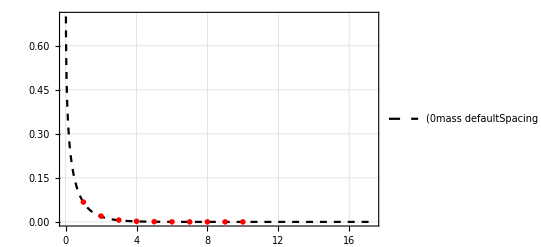

```mathematica
Show[
Plot[
BesselK[0,mass *defaultSpacing*x]/(2Pi),{x,0,Sqrt[3]*nmax},PlotRange->{0,0.7},PlotStyle->{Black,Dashed},PlotTheme->{"Detailed"}
],
ListPlot[
Thread[List[rdist,vv]],PlotStyle->{Red,PointSize[0.05]},
PlotTheme->{"Business"}
]
]
```

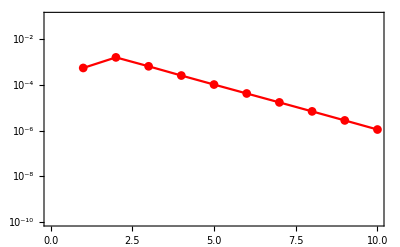

```mathematica
ListLogPlot[
Thread[List[rdist,err]],PlotStyle->{Red,PointSize[0.05]},
Joined->True,PlotMarkers->Automatic,PlotTheme->"Detailed",PlotRange->{10^(-10),10^(-1)}
]
```